# Problem 3 d

```mathematica
ysig=sig;
ytanh[tratio_,bratio_]:=Tanh[(tratio)^-1*bratio+(tratio)^-1*sig];
```

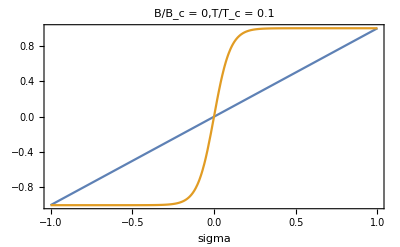

```mathematica
Plot[{ysig,ytanh[0.1,0]},{sig,-1,1},AxesLabel->{sigma},PlotLabel->"B/B_c = 0,T/T_c = 0.1",Axes->True,Frame->True]
```

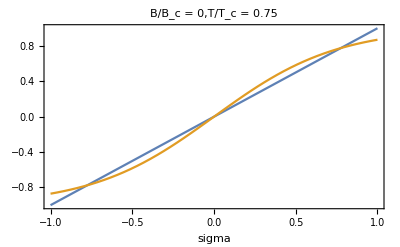

```mathematica
Plot[{ysig,ytanh[0.75,0]},{sig,-1,1},AxesLabel->{sigma},PlotLabel->"B/B_c = 0,T/T_c = 0.75",Axes->True,Frame->True]
```

The two graphs above show that sigma can have a non-trivial solution when T < T_c. Note how the two graphs overlap at places other than zero. This differs from the graphs below, which model T = T_c and T > T_c. In the two cases below, the two graphs only overlap at zero, which is a trivial solution.

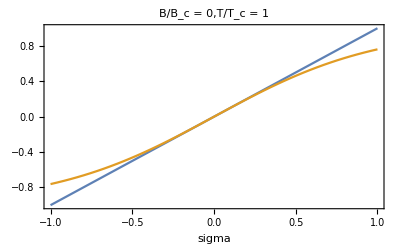

```mathematica
Plot[{ysig,ytanh[1,0]},{sig,-1,1},AxesLabel->{sigma},PlotLabel->"B/B_c = 0,T/T_c = 1",Axes->True,Frame->True]
```

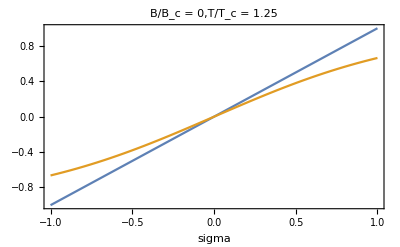

```mathematica
Plot[{ysig,ytanh[1.25,0]},{sig,-1,1},AxesLabel->{sigma},PlotLabel->"B/B_c = 0,T/T_c = 1.25",Axes->True,Frame->True]
```